```mathematica
Quit
```

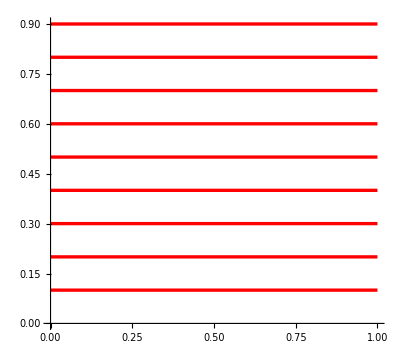

```mathematica
Table[{θ1,C1},{C1,1/10,9/10,1/10}];
Curve1=ParametricPlot[{%},{θ1,0,1},PlotStyle->Directive[Thickness[.006],Red]]
```

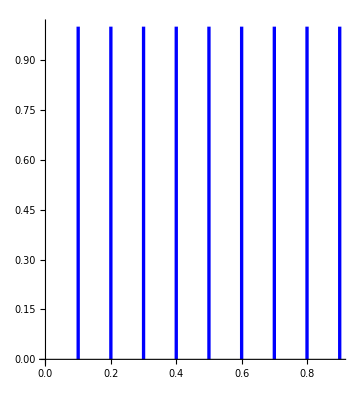

```mathematica
Table[{C2,θ2},{C2,1/10,9/10,1/10}];
Curve2=ParametricPlot[{%},{θ2,0,1},PlotStyle->Directive[Thickness[.006],Blue]]
```

```mathematica
Ref1=ParametricPlot[{X,Y},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,0.618]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Axes->False,Frame->False,PerformanceGoal->"Quality"];
```

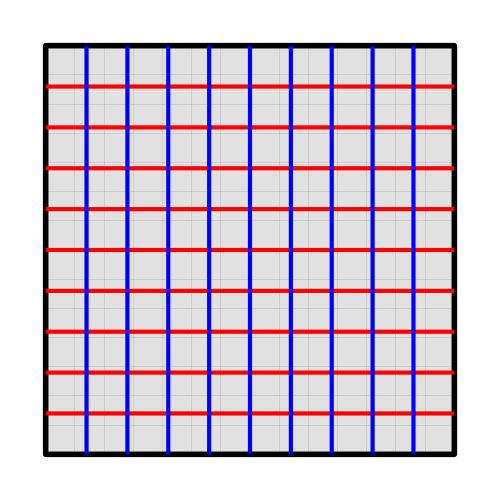

```mathematica
Show[Ref1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

```mathematica
a=5;
```

```mathematica
x0[X_,Y_]:=X
y0[X_,Y_]:=Y
z0[X_,Y_]:=-X+X^2+Y-Y^2+1/2
```

```mathematica
Curve1=ParametricPlot3D[Table[{x0[X,Y0],y0[X,Y0],z0[X,Y0]},{Y0,1/10,9/10,1/10}],{X,0,1},PlotStyle->Directive[Thickness[.005],Red],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Curve2=ParametricPlot3D[Table[{x0[X0,Y],y0[X0,Y],z0[X0,Y]},{X0,1/10,9/10,1/10}],{Y,0,1},PlotStyle->Directive[Thickness[.005],Blue],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,1],Specularity[White,80],Opacity[0.8],Glow[RGBColor[0.618,0.618,1]]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality",PlotRange->All];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

-Graphics3D-

去掉反光

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,1},{Y,0,1},PlotStyle->Directive[RGBColor[0.618,0.618,1],Opacity[0.8]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality",ViewProjection->"Orthographic",(*ColorFunction->White,*)Lighting->{{"Point",White,{1,0,1}},{"Directional",RGBColor[1,1,1],{1,1,4},{{1,1,-4}}}},MaxRecursion-> 10];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->800,PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["Cur.png",Cur1,Background->None]
```

Cur.png